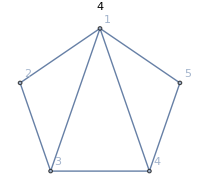
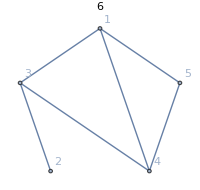
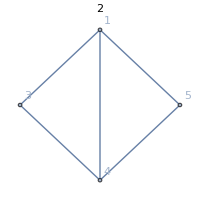
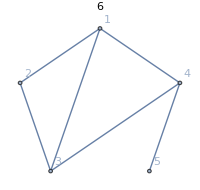
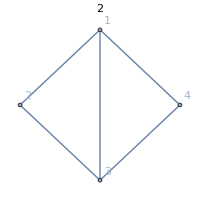
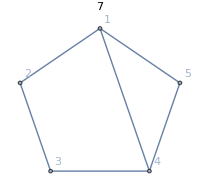
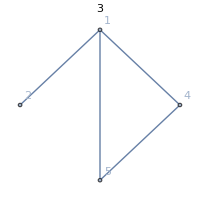
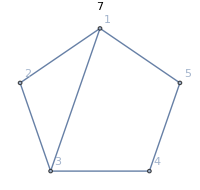
{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 4
 | 
4 | 
4 | 
4 | 
4
2 |  | 4
 | 
4 | 2
2 | 1
3
3 |  |  | 4
 | 
4 | 2
2
4 |  |  |  | 4
 | 
4
5 |  |  |  |  | 4
}full,{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 6
 | 2
4 | 
6 | 
6 | 
6
2 |  | 6
 | 
6 | 2
4 | 1
5
3 |  |  | 6
 | 
6 | 3
3
4 |  |  |  | 6
 | 
6
5 |  |  |  |  | 6
}{EdgeDelete,1<->2},{-Graphics-, | 1 | 3 | 4 | 5
1 | 2
 | 
2 | 
2 | 
2
3 |  | 2
 | 
2 | 1
1
4 |  |  | 2
 | 
2
5 |  |  |  | 2
}{EdgeContract,1<->2}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 6
 | 
6 | 
6 | 
6 | 2
4
2 |  | 6
 | 
6 | 3
3 | 1
5
3 |  |  | 6
 | 
6 | 2
4
4 |  |  |  | 6
 | 
6
5 |  |  |  |  | 6
}{EdgeDelete,1<->5},{-Graphics-, | 1 | 2 | 3 | 4
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
3 |  |  | 2
 | 
2
4 |  |  |  | 2
}{EdgeContract,1<->5}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
 | 
7 | 3
4 | 
7 | 
7
2 |  | 7
 | 
7 | 3
4 | 2
5
3 |  |  | 7
 | 
7 | 2
5
4 |  |  |  | 7
 | 
7
5 |  |  |  |  | 7
}{EdgeDelete,1<->3},{-Graphics-, | 1 | 2 | 4 | 5
1 | 3
 | 
3 | 
3 | 
3
2 |  | 3
 | 1
2 | 1
2
4 |  |  | 3
 | 
3
5 |  |  |  | 3
}{EdgeContract,1<->3}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
 | 
7 | 
7 | 3
4 | 
7
2 |  | 7
 | 
7 | 2
5 | 2
5
3 |  |  | 7
 | 
7 | 3
4
4 |  |  |  | 7
 | 
7
5 |  |  |  |  | 7
}{EdgeDelete,1<->4},{-Graphics-, | 1 | 2 | 3 | 5
1 | 3
 | 
3 | 
3 | 
3
2 |  | 3
 | 
3 | 1
2
3 |  |  | 3
 | 1
2
5 |  |  |  | 3
}{EdgeContract,1<->4}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 6
 | 
6 | 
6 | 
6 | 
6
2 |  | 6
 | 2
4 | 2
4 | 2
4
3 |  |  | 6
 | 
6 | 3
3
4 |  |  |  | 6
 | 
6
5 |  |  |  |  | 6
}{EdgeDelete,2<->3},{-Graphics-, | 1 | 2 | 4 | 5
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
4 |  |  | 2
 | 
2
5 |  |  |  | 2
}{EdgeContract,2<->3}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 6
 | 
6 | 
6 | 
6 | 
6
2 |  | 6
 | 
6 | 2
4 | 2
4
3 |  |  | 6
 | 2
4 | 2
4
4 |  |  |  | 6
 | 
6
5 |  |  |  |  | 6
}{EdgeDelete,3<->4},{-Graphics-, | 1 | 2 | 3 | 5
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
3 |  |  | 2
 | 
2
5 |  |  |  | 2
}{EdgeContract,3<->4}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 6
 | 
6 | 
6 | 
6 | 
6
2 |  | 6
 | 
6 | 3
3 | 2
4
3 |  |  | 6
 | 
6 | 2
4
4 |  |  |  | 6
 | 2
4
5 |  |  |  |  | 6
}{EdgeDelete,4<->5},{-Graphics-, | 1 | 2 | 3 | 4
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
3 |  |  | 2
 | 
2
4 |  |  |  | 2
}{EdgeContract,4<->5}}}

```mathematica
Monitor[
Table[
With[
{g=EdgeAdd[CycleGraph[5],{1<->3,1<->4}]},
ColorMatrixForEdgeOperationMatrix[g,EdgeList[g],{EdgeDelete,EdgeContract}, 
Graph[#,GraphLayout->"TutteEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[#,4]/24,ImageSize->200]&]/. 0->""
],
{m,1,1}
]//Column,
m
]
```

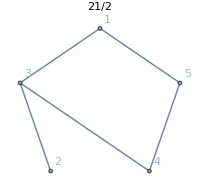
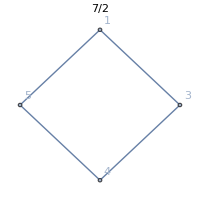
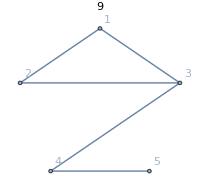
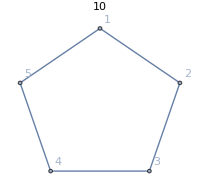
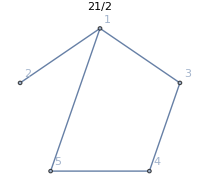
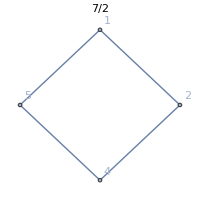
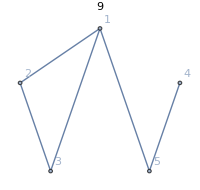
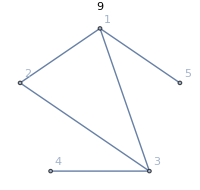
{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
 | 
7 | 
7 | 3
4 | 
7
2 |  | 7
 | 
7 | 2
5 | 2
5
3 |  |  | 7
 | 
7 | 3
4
4 |  |  |  | 7
 | 
7
5 |  |  |  |  | 7
}full,{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 21/2
 | 7/2
7 | 
21/2 | 9/2
6 | 
21/2
2 |  | 21/2
 | 
21/2 | 7/2
7 | 2
17/2
3 |  |  | 21/2
 | 
21/2 | 9/2
6
4 |  |  |  | 21/2
 | 
21/2
5 |  |  |  |  | 21/2
}{EdgeDelete,1<->2},{-Graphics-, | 1 | 3 | 4 | 5
1 | 7/2
 | 
7/2 | 3/2
2 | 
7/2
3 |  | 7/2
 | 
7/2 | 3/2
2
4 |  |  | 7/2
 | 
7/2
5 |  |  |  | 7/2
}{EdgeContract,1<->2}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 9
 | 
9 | 
9 | 3
6 | 2
7
2 |  | 9
 | 
9 | 3
6 | 2
7
3 |  |  | 9
 | 
9 | 3
6
4 |  |  |  | 9
 | 
9
5 |  |  |  |  | 9
}{EdgeDelete,1<->5},{-Graphics-, | 1 | 2 | 3 | 4
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
3 |  |  | 2
 | 
2
4 |  |  |  | 2
}{EdgeContract,1<->5}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 10
 | 
10 | 3
7 | 3
7 | 
10
2 |  | 10
 | 
10 | 3
7 | 3
7
3 |  |  | 10
 | 
10 | 3
7
4 |  |  |  | 10
 | 
10
5 |  |  |  |  | 10
}{EdgeDelete,1<->3},{-Graphics-, | 1 | 2 | 4 | 5
1 | 3
 | 
3 | 
3 | 
3
2 |  | 3
 | 1
2 | 1
2
4 |  |  | 3
 | 
3
5 |  |  |  | 3
}{EdgeContract,1<->3}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 21/2
 | 
21/2 | 
21/2 | 9/2
6 | 
21/2
2 |  | 21/2
 | 7/2
7 | 2
17/2 | 7/2
7
3 |  |  | 21/2
 | 
21/2 | 9/2
6
4 |  |  |  | 21/2
 | 
21/2
5 |  |  |  |  | 21/2
}{EdgeDelete,2<->3},{-Graphics-, | 1 | 2 | 4 | 5
1 | 7/2
 | 
7/2 | 3/2
2 | 
7/2
2 |  | 7/2
 | 
7/2 | 3/2
2
4 |  |  | 7/2
 | 
7/2
5 |  |  |  | 7/2
}{EdgeContract,2<->3}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 9
 | 
9 | 
9 | 3
6 | 
9
2 |  | 9
 | 
9 | 2
7 | 3
6
3 |  |  | 9
 | 2
7 | 3
6
4 |  |  |  | 9
 | 
9
5 |  |  |  |  | 9
}{EdgeDelete,3<->4},{-Graphics-, | 1 | 2 | 3 | 5
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
3 |  |  | 2
 | 
2
5 |  |  |  | 2
}{EdgeContract,3<->4}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 9
 | 
9 | 
9 | 3
6 | 
9
2 |  | 9
 | 
9 | 3
6 | 3
6
3 |  |  | 9
 | 
9 | 3
6
4 |  |  |  | 9
 | 2
7
5 |  |  |  |  | 9
}{EdgeDelete,4<->5},{-Graphics-, | 1 | 2 | 3 | 4
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
3 |  |  | 2
 | 
2
4 |  |  |  | 2
}{EdgeContract,4<->5}}}

```mathematica
Monitor[
Table[
With[
{g=EdgeAdd[CycleGraph[5],{1<->3}]},
ColorMatrixForEdgeOperationMatrix[g,EdgeList[g],{EdgeDelete,EdgeContract}, 
Graph[#,GraphLayout->"TutteEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[#,4]/24,ImageSize->200]&]/. 0->""
],
{m,1,1}
]//Column,
m
]
```

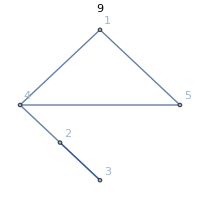
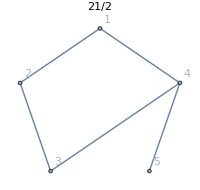
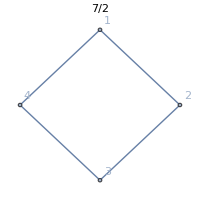
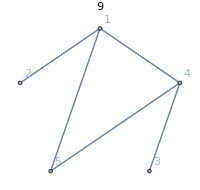
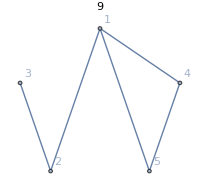
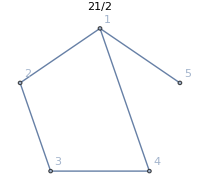
{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
 | 
7 | 3
4 | 
7 | 
7
2 |  | 7
 | 
7 | 3
4 | 2
5
3 |  |  | 7
 | 
7 | 2
5
4 |  |  |  | 7
 | 
7
5 |  |  |  |  | 7
}full,{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 9
 | 2
7 | 3
6 | 
9 | 
9
2 |  | 9
 | 
9 | 3
6 | 2
7
3 |  |  | 9
 | 
9 | 3
6
4 |  |  |  | 9
 | 
9
5 |  |  |  |  | 9
}{EdgeDelete,1<->2},{-Graphics-, | 1 | 3 | 4 | 5
1 | 2
 | 
2 | 
2 | 
2
3 |  | 2
 | 
2 | 1
1
4 |  |  | 2
 | 
2
5 |  |  |  | 2
}{EdgeContract,1<->2}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 21/2
 | 
21/2 | 9/2
6 | 
21/2 | 7/2
7
2 |  | 21/2
 | 
21/2 | 9/2
6 | 2
17/2
3 |  |  | 21/2
 | 
21/2 | 7/2
7
4 |  |  |  | 21/2
 | 
21/2
5 |  |  |  |  | 21/2
}{EdgeDelete,1<->5},{-Graphics-, | 1 | 2 | 3 | 4
1 | 7/2
 | 
7/2 | 3/2
2 | 
7/2
2 |  | 7/2
 | 
7/2 | 3/2
2
3 |  |  | 7/2
 | 
7/2
4 |  |  |  | 7/2
}{EdgeContract,1<->5}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 10
 | 
10 | 3
7 | 3
7 | 
10
2 |  | 10
 | 
10 | 3
7 | 3
7
3 |  |  | 10
 | 
10 | 3
7
4 |  |  |  | 10
 | 
10
5 |  |  |  |  | 10
}{EdgeDelete,1<->4},{-Graphics-, | 1 | 2 | 3 | 5
1 | 3
 | 
3 | 
3 | 
3
2 |  | 3
 | 
3 | 1
2
3 |  |  | 3
 | 1
2
5 |  |  |  | 3
}{EdgeContract,1<->4}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 9
 | 
9 | 3
6 | 
9 | 
9
2 |  | 9
 | 2
7 | 3
6 | 3
6
3 |  |  | 9
 | 
9 | 3
6
4 |  |  |  | 9
 | 
9
5 |  |  |  |  | 9
}{EdgeDelete,2<->3},{-Graphics-, | 1 | 2 | 4 | 5
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
4 |  |  | 2
 | 
2
5 |  |  |  | 2
}{EdgeContract,2<->3}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 9
 | 
9 | 3
6 | 
9 | 
9
2 |  | 9
 | 
9 | 3
6 | 3
6
3 |  |  | 9
 | 2
7 | 2
7
4 |  |  |  | 9
 | 
9
5 |  |  |  |  | 9
}{EdgeDelete,3<->4},{-Graphics-, | 1 | 2 | 3 | 5
1 | 2
 | 
2 | 
2 | 
2
2 |  | 2
 | 
2 | 1
1
3 |  |  | 2
 | 
2
5 |  |  |  | 2
}{EdgeContract,3<->4}},{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 21/2
 | 
21/2 | 9/2
6 | 
21/2 | 
21/2
2 |  | 21/2
 | 
21/2 | 9/2
6 | 7/2
7
3 |  |  | 21/2
 | 
21/2 | 2
17/2
4 |  |  |  | 21/2
 | 7/2
7
5 |  |  |  |  | 21/2
}{EdgeDelete,4<->5},{-Graphics-, | 1 | 2 | 3 | 4
1 | 7/2
 | 
7/2 | 3/2
2 | 
7/2
2 |  | 7/2
 | 
7/2 | 3/2
2
3 |  |  | 7/2
 | 
7/2
4 |  |  |  | 7/2
}{EdgeContract,4<->5}}}

```mathematica
Monitor[
Table[
With[
{g=EdgeAdd[CycleGraph[5],{1<->4}]},
ColorMatrixForEdgeOperationMatrix[g,EdgeList[g],{EdgeDelete,EdgeContract}, 
Graph[#,GraphLayout->"TutteEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[#,4]/24,ImageSize->200]&]/. 0->""
],
{m,1,1}
]//Column,
m
]
```